```mathematica
ClearAll["Global'*"]
```

## Einführung in die Computer Algebra - 2024 - Übungsblatt 2

### 1. Aufgabe :

Zeigen Sie mit Hilfe von Mathematica, dass:  		
a- 		 
b-

Hinweis: Nützliche Befehle Dot[ ], Cross[ ], == , Simplify .

```mathematica
(* Define the Vectors*)
a = {a1,a2,a3}
b={b1,b2,b3}
c = {c1,c2,c3}
```

{a1,a2,a3}

{b1,b2,b3}

{c1,c2,c3}

```mathematica
(* Teil a*)
cross1=Cross[a,Cross[b,c]]
cross2=Cross[b,Cross[c,a]]
cross3 = Cross[c,Cross[a,b]]
```

{-a2 b2 c1-a3 b3 c1+a2 b1 c2+a3 b1 c3,a1 b2 c1-a1 b1 c2-a3 b3 c2+a3 b2 c3,a1 b3 c1+a2 b3 c2-a1 b1 c3-a2 b2 c3}

{a2 b2 c1+a3 b3 c1-a1 b2 c2-a1 b3 c3,-a2 b1 c1+a1 b1 c2+a3 b3 c2-a2 b3 c3,-a3 b1 c1-a3 b2 c2+a1 b1 c3+a2 b2 c3}

{-a2 b1 c2+a1 b2 c2-a3 b1 c3+a1 b3 c3,a2 b1 c1-a1 b2 c1-a3 b2 c3+a2 b3 c3,a3 b1 c1-a1 b3 c1+a3 b2 c2-a2 b3 c2}

```mathematica
Simplify[cross1+cross2+cross3== {0,0,0}]
```

True

```mathematica
(*Teil b*)
dot1=(a.c)b
dot2=Dot[a,b]c
```

{b1 (a1 c1+a2 c2+a3 c3),b2 (a1 c1+a2 c2+a3 c3),b3 (a1 c1+a2 c2+a3 c3)}

{(a1 b1+a2 b2+a3 b3) c1,(a1 b1+a2 b2+a3 b3) c2,(a1 b1+a2 b2+a3 b3) c3}

```mathematica
Simplify[cross1==dot1-dot2]
```

True

### 2. Aufgabe:

Lösen Sie die Laplace Gleichung    in Zylinderkoordinaten, mit den Randbedingungen :  und  .   Die Funktion  ist nur von   abhängig.
Plotten Sie ihr Ergebnis.

Hinweis: Nützliche Befehle: DSolve[ ] , Laplacian[ ].

ψ'[ρ]/ρ+ψ''[ρ]==0

{{ψ[ρ]→-4 (Log[4]-Log[ρ])}}

{{ψ[ρ]→-4 (Log[4]-Log[ρ])}}

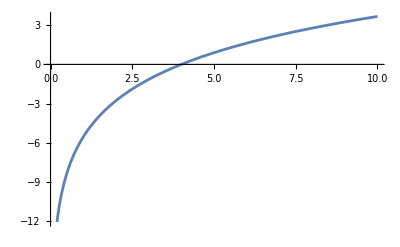

```mathematica
Clear[ψ,ρ]
dgl1 = Laplacian[ψ[ρ],{ρ,ϕ,z},"Cylindrical"] == 0
DSolve[{dgl1,ψ[4]==0,ψ'[4]==1},ψ[ρ],ρ]
sol = DSolve[{dgl1,ψ[4]==0,ψ'[4]==1},ψ[ρ],ρ]
Plot[Evaluate[ψ[ρ]/.sol],{ρ,0,10}]
```

### 3. Aufgabe

Berechnen Sie den Logarithmus des Fakultät der ersten 35 natürlich Zahlen exakt und mit Hilfe der Stirling-Formel:
				
Plotten Sie anschließend die relativen Abweichungen :
				
				
Starten Sie mit n=2.

Hinweis: Nützliche Befehle: Table[ ], ListPlot[ ].

{0.651806,1.76408,3.15726,4.77085,6.56538,8.51326,10.5942,12.7926,15.0961,17.4947,19.9803,22.5458,25.1853,27.8937,30.6667,33.5002,36.3908,39.3355,42.3315,45.3762,48.4674,51.6031,54.7813,58.0003,61.2585,64.5545,67.8868,71.2542,74.6555,78.0895,81.5554,85.0519,88.5784,92.1338}

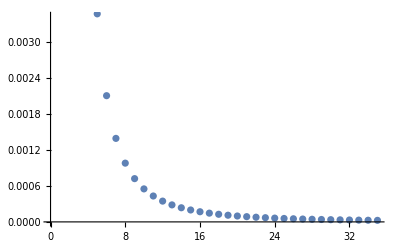

```mathematica
stirlingvalues = Table[n Log[n]-n+1/2 Log[2 Pi n],{n,2,35}] // N
koord := Table[{n,(Log[n!]-stirlingvalues[[n-1]])/Log[n!]},{n,2,35}]
ListPlot[koord]
```

### 4. Aufgabe:

Gegeben eine Liste mit Paaren {i,j}, erzeugen Sie eine Liste mit dem Produkt i*j. Vergleichen Sie die Laufzeit der naiven Umsetzung mit einem For[ ]-Loop mit der Laufzeit für die Umsetzung mit  Table[ ] und schließlich mit Map[ ].

Hinweis: Nützliche Befehle: AbsoluteTiming[ ]

```mathematica
(*Liste mit Paaren {i,j}*)
Listij = Tuples[Range[50],2];
Length[Listij]
```

2500

```mathematica
(*Using For*)
AbsoluteTiming[
productFor=Module[{results={}},
For[i = 1, i <= Length[Listij], i++,
AppendTo[results,Listij[[i,1]]*Listij[[i,2]]]
]
]
]
```

{0.0298657,Null}

```mathematica
(*Using Table*)
AbsoluteTiming[
productTable =Table[Listij[[i,1]]*Listij[[i,2]],{i,Length[Listij]}]
]
```

{0.0004402,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100,3,6,9,12,15,18,21,24,27,30,33,36,39,42,45,48,51,54,57,60,63,66,69,72,75,78,81,84,87,90,93,96,99,102,105,108,111,114,117,120,123,126,129,132,135,138,141,144,147,150,4,8,12,16,20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160,164,168,172,176,180,184,188,192,196,200,5,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100,105,110,115,120,125,130,135,140,145,150,155,160,165,170,175,180,185,190,195,200,205,210,215,220,225,230,235,240,245,250,6,12,18,24,30,36,42,48,54,60,66,72,78,84,90,96,102,108,114,120,126,132,138,144,150,156,162,168,174,180,186,192,198,204,210,216,222,228,234,240,246,252,258,264,270,276,282,288,294,300,7,14,21,28,35,42,49,56,63,70,77,84,91,98,105,112,119,126,133,140,147,154,161,168,175,182,189,196,203,210,217,224,231,238,245,252,259,266,273,280,287,294,301,308,315,322,329,336,343,350,8,16,24,32,40,48,56,64,72,80,88,96,104,112,120,128,136,144,152,160,168,176,184,192,200,208,216,224,232,240,248,256,264,272,280,288,296,304,312,320,328,336,344,352,360,368,376,384,392,400,9,18,27,36,45,54,63,72,81,90,99,108,117,126,135,144,153,162,171,180,189,198,207,216,225,234,243,252,261,270,279,288,297,306,315,324,333,342,351,360,369,378,387,396,405,414,423,432,441,450,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220,230,240,250,260,270,280,290,300,310,320,330,340,350,360,370,380,390,400,410,420,430,440,450,460,470,480,490,500,11,22,33,44,55,66,77,88,99,110,121,132,143,154,165,176,187,198,209,220,231,242,253,264,275,286,297,308,319,330,341,352,363,374,385,396,407,418,429,440,451,462,473,484,495,506,517,528,539,550,12,24,36,48,60,72,84,96,108,120,132,144,156,168,180,192,204,216,228,240,252,264,276,288,300,312,324,336,348,360,372,384,396,408,420,432,444,456,468,480,492,504,516,528,540,552,564,576,588,600,13,26,39,52,65,78,91,104,117,130,143,156,169,182,195,208,221,234,247,260,273,286,299,312,325,338,351,364,377,390,403,416,429,442,455,468,481,494,507,520,533,546,559,572,585,598,611,624,637,650,14,28,42,56,70,84,98,112,126,140,154,168,182,196,210,224,238,252,266,280,294,308,322,336,350,364,378,392,406,420,434,448,462,476,490,504,518,532,546,560,574,588,602,616,630,644,658,672,686,700,15,30,45,60,75,90,105,120,135,150,165,180,195,210,225,240,255,270,285,300,315,330,345,360,375,390,405,420,435,450,465,480,495,510,525,540,555,570,585,600,615,630,645,660,675,690,705,720,735,750,16,32,48,64,80,96,112,128,144,160,176,192,208,224,240,256,272,288,304,320,336,352,368,384,400,416,432,448,464,480,496,512,528,544,560,576,592,608,624,640,656,672,688,704,720,736,752,768,784,800,17,34,51,68,85,102,119,136,153,170,187,204,221,238,255,272,289,306,323,340,357,374,391,408,425,442,459,476,493,510,527,544,561,578,595,612,629,646,663,680,697,714,731,748,765,782,799,816,833,850,18,36,54,72,90,108,126,144,162,180,198,216,234,252,270,288,306,324,342,360,378,396,414,432,450,468,486,504,522,540,558,576,594,612,630,648,666,684,702,720,738,756,774,792,810,828,846,864,882,900,19,38,57,76,95,114,133,152,171,190,209,228,247,266,285,304,323,342,361,380,399,418,437,456,475,494,513,532,551,570,589,608,627,646,665,684,703,722,741,760,779,798,817,836,855,874,893,912,931,950,20,40,60,80,100,120,140,160,180,200,220,240,260,280,300,320,340,360,380,400,420,440,460,480,500,520,540,560,580,600,620,640,660,680,700,720,740,760,780,800,820,840,860,880,900,920,940,960,980,1000,21,42,63,84,105,126,147,168,189,210,231,252,273,294,315,336,357,378,399,420,441,462,483,504,525,546,567,588,609,630,651,672,693,714,735,756,777,798,819,840,861,882,903,924,945,966,987,1008,1029,1050,22,44,66,88,110,132,154,176,198,220,242,264,286,308,330,352,374,396,418,440,462,484,506,528,550,572,594,616,638,660,682,704,726,748,770,792,814,836,858,880,902,924,946,968,990,1012,1034,1056,1078,1100,23,46,69,92,115,138,161,184,207,230,253,276,299,322,345,368,391,414,437,460,483,506,529,552,575,598,621,644,667,690,713,736,759,782,805,828,851,874,897,920,943,966,989,1012,1035,1058,1081,1104,1127,1150,24,48,72,96,120,144,168,192,216,240,264,288,312,336,360,384,408,432,456,480,504,528,552,576,600,624,648,672,696,720,744,768,792,816,840,864,888,912,936,960,984,1008,1032,1056,1080,1104,1128,1152,1176,1200,25,50,75,100,125,150,175,200,225,250,275,300,325,350,375,400,425,450,475,500,525,550,575,600,625,650,675,700,725,750,775,800,825,850,875,900,925,950,975,1000,1025,1050,1075,1100,1125,1150,1175,1200,1225,1250,26,52,78,104,130,156,182,208,234,260,286,312,338,364,390,416,442,468,494,520,546,572,598,624,650,676,702,728,754,780,806,832,858,884,910,936,962,988,1014,1040,1066,1092,1118,1144,1170,1196,1222,1248,1274,1300,27,54,81,108,135,162,189,216,243,270,297,324,351,378,405,432,459,486,513,540,567,594,621,648,675,702,729,756,783,810,837,864,891,918,945,972,999,1026,1053,1080,1107,1134,1161,1188,1215,1242,1269,1296,1323,1350,28,56,84,112,140,168,196,224,252,280,308,336,364,392,420,448,476,504,532,560,588,616,644,672,700,728,756,784,812,840,868,896,924,952,980,1008,1036,1064,1092,1120,1148,1176,1204,1232,1260,1288,1316,1344,1372,1400,29,58,87,116,145,174,203,232,261,290,319,348,377,406,435,464,493,522,551,580,609,638,667,696,725,754,783,812,841,870,899,928,957,986,1015,1044,1073,1102,1131,1160,1189,1218,1247,1276,1305,1334,1363,1392,1421,1450,30,60,90,120,150,180,210,240,270,300,330,360,390,420,450,480,510,540,570,600,630,660,690,720,750,780,810,840,870,900,930,960,990,1020,1050,1080,1110,1140,1170,1200,1230,1260,1290,1320,1350,1380,1410,1440,1470,1500,31,62,93,124,155,186,217,248,279,310,341,372,403,434,465,496,527,558,589,620,651,682,713,744,775,806,837,868,899,930,961,992,1023,1054,1085,1116,1147,1178,1209,1240,1271,1302,1333,1364,1395,1426,1457,1488,1519,1550,32,64,96,128,160,192,224,256,288,320,352,384,416,448,480,512,544,576,608,640,672,704,736,768,800,832,864,896,928,960,992,1024,1056,1088,1120,1152,1184,1216,1248,1280,1312,1344,1376,1408,1440,1472,1504,1536,1568,1600,33,66,99,132,165,198,231,264,297,330,363,396,429,462,495,528,561,594,627,660,693,726,759,792,825,858,891,924,957,990,1023,1056,1089,1122,1155,1188,1221,1254,1287,1320,1353,1386,1419,1452,1485,1518,1551,1584,1617,1650,34,68,102,136,170,204,238,272,306,340,374,408,442,476,510,544,578,612,646,680,714,748,782,816,850,884,918,952,986,1020,1054,1088,1122,1156,1190,1224,1258,1292,1326,1360,1394,1428,1462,1496,1530,1564,1598,1632,1666,1700,35,70,105,140,175,210,245,280,315,350,385,420,455,490,525,560,595,630,665,700,735,770,805,840,875,910,945,980,1015,1050,1085,1120,1155,1190,1225,1260,1295,1330,1365,1400,1435,1470,1505,1540,1575,1610,1645,1680,1715,1750,36,72,108,144,180,216,252,288,324,360,396,432,468,504,540,576,612,648,684,720,756,792,828,864,900,936,972,1008,1044,1080,1116,1152,1188,1224,1260,1296,1332,1368,1404,1440,1476,1512,1548,1584,1620,1656,1692,1728,1764,1800,37,74,111,148,185,222,259,296,333,370,407,444,481,518,555,592,629,666,703,740,777,814,851,888,925,962,999,1036,1073,1110,1147,1184,1221,1258,1295,1332,1369,1406,1443,1480,1517,1554,1591,1628,1665,1702,1739,1776,1813,1850,38,76,114,152,190,228,266,304,342,380,418,456,494,532,570,608,646,684,722,760,798,836,874,912,950,988,1026,1064,1102,1140,1178,1216,1254,1292,1330,1368,1406,1444,1482,1520,1558,1596,1634,1672,1710,1748,1786,1824,1862,1900,39,78,117,156,195,234,273,312,351,390,429,468,507,546,585,624,663,702,741,780,819,858,897,936,975,1014,1053,1092,1131,1170,1209,1248,1287,1326,1365,1404,1443,1482,1521,1560,1599,1638,1677,1716,1755,1794,1833,1872,1911,1950,40,80,120,160,200,240,280,320,360,400,440,480,520,560,600,640,680,720,760,800,840,880,920,960,1000,1040,1080,1120,1160,1200,1240,1280,1320,1360,1400,1440,1480,1520,1560,1600,1640,1680,1720,1760,1800,1840,1880,1920,1960,2000,41,82,123,164,205,246,287,328,369,410,451,492,533,574,615,656,697,738,779,820,861,902,943,984,1025,1066,1107,1148,1189,1230,1271,1312,1353,1394,1435,1476,1517,1558,1599,1640,1681,1722,1763,1804,1845,1886,1927,1968,2009,2050,42,84,126,168,210,252,294,336,378,420,462,504,546,588,630,672,714,756,798,840,882,924,966,1008,1050,1092,1134,1176,1218,1260,1302,1344,1386,1428,1470,1512,1554,1596,1638,1680,1722,1764,1806,1848,1890,1932,1974,2016,2058,2100,43,86,129,172,215,258,301,344,387,430,473,516,559,602,645,688,731,774,817,860,903,946,989,1032,1075,1118,1161,1204,1247,1290,1333,1376,1419,1462,1505,1548,1591,1634,1677,1720,1763,1806,1849,1892,1935,1978,2021,2064,2107,2150,44,88,132,176,220,264,308,352,396,440,484,528,572,616,660,704,748,792,836,880,924,968,1012,1056,1100,1144,1188,1232,1276,1320,1364,1408,1452,1496,1540,1584,1628,1672,1716,1760,1804,1848,1892,1936,1980,2024,2068,2112,2156,2200,45,90,135,180,225,270,315,360,405,450,495,540,585,630,675,720,765,810,855,900,945,990,1035,1080,1125,1170,1215,1260,1305,1350,1395,1440,1485,1530,1575,1620,1665,1710,1755,1800,1845,1890,1935,1980,2025,2070,2115,2160,2205,2250,46,92,138,184,230,276,322,368,414,460,506,552,598,644,690,736,782,828,874,920,966,1012,1058,1104,1150,1196,1242,1288,1334,1380,1426,1472,1518,1564,1610,1656,1702,1748,1794,1840,1886,1932,1978,2024,2070,2116,2162,2208,2254,2300,47,94,141,188,235,282,329,376,423,470,517,564,611,658,705,752,799,846,893,940,987,1034,1081,1128,1175,1222,1269,1316,1363,1410,1457,1504,1551,1598,1645,1692,1739,1786,1833,1880,1927,1974,2021,2068,2115,2162,2209,2256,2303,2350,48,96,144,192,240,288,336,384,432,480,528,576,624,672,720,768,816,864,912,960,1008,1056,1104,1152,1200,1248,1296,1344,1392,1440,1488,1536,1584,1632,1680,1728,1776,1824,1872,1920,1968,2016,2064,2112,2160,2208,2256,2304,2352,2400,49,98,147,196,245,294,343,392,441,490,539,588,637,686,735,784,833,882,931,980,1029,1078,1127,1176,1225,1274,1323,1372,1421,1470,1519,1568,1617,1666,1715,1764,1813,1862,1911,1960,2009,2058,2107,2156,2205,2254,2303,2352,2401,2450,50,100,150,200,250,300,350,400,450,500,550,600,650,700,750,800,850,900,950,1000,1050,1100,1150,1200,1250,1300,1350,1400,1450,1500,1550,1600,1650,1700,1750,1800,1850,1900,1950,2000,2050,2100,2150,2200,2250,2300,2350,2400,2450,2500}}

```mathematica
(*Using Map*)
AbsoluteTiming[
productMap = Map[Times @@ #&,Listij]
]
```

{0.0006602,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100,3,6,9,12,15,18,21,24,27,30,33,36,39,42,45,48,51,54,57,60,63,66,69,72,75,78,81,84,87,90,93,96,99,102,105,108,111,114,117,120,123,126,129,132,135,138,141,144,147,150,4,8,12,16,20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160,164,168,172,176,180,184,188,192,196,200,5,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100,105,110,115,120,125,130,135,140,145,150,155,160,165,170,175,180,185,190,195,200,205,210,215,220,225,230,235,240,245,250,6,12,18,24,30,36,42,48,54,60,66,72,78,84,90,96,102,108,114,120,126,132,138,144,150,156,162,168,174,180,186,192,198,204,210,216,222,228,234,240,246,252,258,264,270,276,282,288,294,300,7,14,21,28,35,42,49,56,63,70,77,84,91,98,105,112,119,126,133,140,147,154,161,168,175,182,189,196,203,210,217,224,231,238,245,252,259,266,273,280,287,294,301,308,315,322,329,336,343,350,8,16,24,32,40,48,56,64,72,80,88,96,104,112,120,128,136,144,152,160,168,176,184,192,200,208,216,224,232,240,248,256,264,272,280,288,296,304,312,320,328,336,344,352,360,368,376,384,392,400,9,18,27,36,45,54,63,72,81,90,99,108,117,126,135,144,153,162,171,180,189,198,207,216,225,234,243,252,261,270,279,288,297,306,315,324,333,342,351,360,369,378,387,396,405,414,423,432,441,450,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220,230,240,250,260,270,280,290,300,310,320,330,340,350,360,370,380,390,400,410,420,430,440,450,460,470,480,490,500,11,22,33,44,55,66,77,88,99,110,121,132,143,154,165,176,187,198,209,220,231,242,253,264,275,286,297,308,319,330,341,352,363,374,385,396,407,418,429,440,451,462,473,484,495,506,517,528,539,550,12,24,36,48,60,72,84,96,108,120,132,144,156,168,180,192,204,216,228,240,252,264,276,288,300,312,324,336,348,360,372,384,396,408,420,432,444,456,468,480,492,504,516,528,540,552,564,576,588,600,13,26,39,52,65,78,91,104,117,130,143,156,169,182,195,208,221,234,247,260,273,286,299,312,325,338,351,364,377,390,403,416,429,442,455,468,481,494,507,520,533,546,559,572,585,598,611,624,637,650,14,28,42,56,70,84,98,112,126,140,154,168,182,196,210,224,238,252,266,280,294,308,322,336,350,364,378,392,406,420,434,448,462,476,490,504,518,532,546,560,574,588,602,616,630,644,658,672,686,700,15,30,45,60,75,90,105,120,135,150,165,180,195,210,225,240,255,270,285,300,315,330,345,360,375,390,405,420,435,450,465,480,495,510,525,540,555,570,585,600,615,630,645,660,675,690,705,720,735,750,16,32,48,64,80,96,112,128,144,160,176,192,208,224,240,256,272,288,304,320,336,352,368,384,400,416,432,448,464,480,496,512,528,544,560,576,592,608,624,640,656,672,688,704,720,736,752,768,784,800,17,34,51,68,85,102,119,136,153,170,187,204,221,238,255,272,289,306,323,340,357,374,391,408,425,442,459,476,493,510,527,544,561,578,595,612,629,646,663,680,697,714,731,748,765,782,799,816,833,850,18,36,54,72,90,108,126,144,162,180,198,216,234,252,270,288,306,324,342,360,378,396,414,432,450,468,486,504,522,540,558,576,594,612,630,648,666,684,702,720,738,756,774,792,810,828,846,864,882,900,19,38,57,76,95,114,133,152,171,190,209,228,247,266,285,304,323,342,361,380,399,418,437,456,475,494,513,532,551,570,589,608,627,646,665,684,703,722,741,760,779,798,817,836,855,874,893,912,931,950,20,40,60,80,100,120,140,160,180,200,220,240,260,280,300,320,340,360,380,400,420,440,460,480,500,520,540,560,580,600,620,640,660,680,700,720,740,760,780,800,820,840,860,880,900,920,940,960,980,1000,21,42,63,84,105,126,147,168,189,210,231,252,273,294,315,336,357,378,399,420,441,462,483,504,525,546,567,588,609,630,651,672,693,714,735,756,777,798,819,840,861,882,903,924,945,966,987,1008,1029,1050,22,44,66,88,110,132,154,176,198,220,242,264,286,308,330,352,374,396,418,440,462,484,506,528,550,572,594,616,638,660,682,704,726,748,770,792,814,836,858,880,902,924,946,968,990,1012,1034,1056,1078,1100,23,46,69,92,115,138,161,184,207,230,253,276,299,322,345,368,391,414,437,460,483,506,529,552,575,598,621,644,667,690,713,736,759,782,805,828,851,874,897,920,943,966,989,1012,1035,1058,1081,1104,1127,1150,24,48,72,96,120,144,168,192,216,240,264,288,312,336,360,384,408,432,456,480,504,528,552,576,600,624,648,672,696,720,744,768,792,816,840,864,888,912,936,960,984,1008,1032,1056,1080,1104,1128,1152,1176,1200,25,50,75,100,125,150,175,200,225,250,275,300,325,350,375,400,425,450,475,500,525,550,575,600,625,650,675,700,725,750,775,800,825,850,875,900,925,950,975,1000,1025,1050,1075,1100,1125,1150,1175,1200,1225,1250,26,52,78,104,130,156,182,208,234,260,286,312,338,364,390,416,442,468,494,520,546,572,598,624,650,676,702,728,754,780,806,832,858,884,910,936,962,988,1014,1040,1066,1092,1118,1144,1170,1196,1222,1248,1274,1300,27,54,81,108,135,162,189,216,243,270,297,324,351,378,405,432,459,486,513,540,567,594,621,648,675,702,729,756,783,810,837,864,891,918,945,972,999,1026,1053,1080,1107,1134,1161,1188,1215,1242,1269,1296,1323,1350,28,56,84,112,140,168,196,224,252,280,308,336,364,392,420,448,476,504,532,560,588,616,644,672,700,728,756,784,812,840,868,896,924,952,980,1008,1036,1064,1092,1120,1148,1176,1204,1232,1260,1288,1316,1344,1372,1400,29,58,87,116,145,174,203,232,261,290,319,348,377,406,435,464,493,522,551,580,609,638,667,696,725,754,783,812,841,870,899,928,957,986,1015,1044,1073,1102,1131,1160,1189,1218,1247,1276,1305,1334,1363,1392,1421,1450,30,60,90,120,150,180,210,240,270,300,330,360,390,420,450,480,510,540,570,600,630,660,690,720,750,780,810,840,870,900,930,960,990,1020,1050,1080,1110,1140,1170,1200,1230,1260,1290,1320,1350,1380,1410,1440,1470,1500,31,62,93,124,155,186,217,248,279,310,341,372,403,434,465,496,527,558,589,620,651,682,713,744,775,806,837,868,899,930,961,992,1023,1054,1085,1116,1147,1178,1209,1240,1271,1302,1333,1364,1395,1426,1457,1488,1519,1550,32,64,96,128,160,192,224,256,288,320,352,384,416,448,480,512,544,576,608,640,672,704,736,768,800,832,864,896,928,960,992,1024,1056,1088,1120,1152,1184,1216,1248,1280,1312,1344,1376,1408,1440,1472,1504,1536,1568,1600,33,66,99,132,165,198,231,264,297,330,363,396,429,462,495,528,561,594,627,660,693,726,759,792,825,858,891,924,957,990,1023,1056,1089,1122,1155,1188,1221,1254,1287,1320,1353,1386,1419,1452,1485,1518,1551,1584,1617,1650,34,68,102,136,170,204,238,272,306,340,374,408,442,476,510,544,578,612,646,680,714,748,782,816,850,884,918,952,986,1020,1054,1088,1122,1156,1190,1224,1258,1292,1326,1360,1394,1428,1462,1496,1530,1564,1598,1632,1666,1700,35,70,105,140,175,210,245,280,315,350,385,420,455,490,525,560,595,630,665,700,735,770,805,840,875,910,945,980,1015,1050,1085,1120,1155,1190,1225,1260,1295,1330,1365,1400,1435,1470,1505,1540,1575,1610,1645,1680,1715,1750,36,72,108,144,180,216,252,288,324,360,396,432,468,504,540,576,612,648,684,720,756,792,828,864,900,936,972,1008,1044,1080,1116,1152,1188,1224,1260,1296,1332,1368,1404,1440,1476,1512,1548,1584,1620,1656,1692,1728,1764,1800,37,74,111,148,185,222,259,296,333,370,407,444,481,518,555,592,629,666,703,740,777,814,851,888,925,962,999,1036,1073,1110,1147,1184,1221,1258,1295,1332,1369,1406,1443,1480,1517,1554,1591,1628,1665,1702,1739,1776,1813,1850,38,76,114,152,190,228,266,304,342,380,418,456,494,532,570,608,646,684,722,760,798,836,874,912,950,988,1026,1064,1102,1140,1178,1216,1254,1292,1330,1368,1406,1444,1482,1520,1558,1596,1634,1672,1710,1748,1786,1824,1862,1900,39,78,117,156,195,234,273,312,351,390,429,468,507,546,585,624,663,702,741,780,819,858,897,936,975,1014,1053,1092,1131,1170,1209,1248,1287,1326,1365,1404,1443,1482,1521,1560,1599,1638,1677,1716,1755,1794,1833,1872,1911,1950,40,80,120,160,200,240,280,320,360,400,440,480,520,560,600,640,680,720,760,800,840,880,920,960,1000,1040,1080,1120,1160,1200,1240,1280,1320,1360,1400,1440,1480,1520,1560,1600,1640,1680,1720,1760,1800,1840,1880,1920,1960,2000,41,82,123,164,205,246,287,328,369,410,451,492,533,574,615,656,697,738,779,820,861,902,943,984,1025,1066,1107,1148,1189,1230,1271,1312,1353,1394,1435,1476,1517,1558,1599,1640,1681,1722,1763,1804,1845,1886,1927,1968,2009,2050,42,84,126,168,210,252,294,336,378,420,462,504,546,588,630,672,714,756,798,840,882,924,966,1008,1050,1092,1134,1176,1218,1260,1302,1344,1386,1428,1470,1512,1554,1596,1638,1680,1722,1764,1806,1848,1890,1932,1974,2016,2058,2100,43,86,129,172,215,258,301,344,387,430,473,516,559,602,645,688,731,774,817,860,903,946,989,1032,1075,1118,1161,1204,1247,1290,1333,1376,1419,1462,1505,1548,1591,1634,1677,1720,1763,1806,1849,1892,1935,1978,2021,2064,2107,2150,44,88,132,176,220,264,308,352,396,440,484,528,572,616,660,704,748,792,836,880,924,968,1012,1056,1100,1144,1188,1232,1276,1320,1364,1408,1452,1496,1540,1584,1628,1672,1716,1760,1804,1848,1892,1936,1980,2024,2068,2112,2156,2200,45,90,135,180,225,270,315,360,405,450,495,540,585,630,675,720,765,810,855,900,945,990,1035,1080,1125,1170,1215,1260,1305,1350,1395,1440,1485,1530,1575,1620,1665,1710,1755,1800,1845,1890,1935,1980,2025,2070,2115,2160,2205,2250,46,92,138,184,230,276,322,368,414,460,506,552,598,644,690,736,782,828,874,920,966,1012,1058,1104,1150,1196,1242,1288,1334,1380,1426,1472,1518,1564,1610,1656,1702,1748,1794,1840,1886,1932,1978,2024,2070,2116,2162,2208,2254,2300,47,94,141,188,235,282,329,376,423,470,517,564,611,658,705,752,799,846,893,940,987,1034,1081,1128,1175,1222,1269,1316,1363,1410,1457,1504,1551,1598,1645,1692,1739,1786,1833,1880,1927,1974,2021,2068,2115,2162,2209,2256,2303,2350,48,96,144,192,240,288,336,384,432,480,528,576,624,672,720,768,816,864,912,960,1008,1056,1104,1152,1200,1248,1296,1344,1392,1440,1488,1536,1584,1632,1680,1728,1776,1824,1872,1920,1968,2016,2064,2112,2160,2208,2256,2304,2352,2400,49,98,147,196,245,294,343,392,441,490,539,588,637,686,735,784,833,882,931,980,1029,1078,1127,1176,1225,1274,1323,1372,1421,1470,1519,1568,1617,1666,1715,1764,1813,1862,1911,1960,2009,2058,2107,2156,2205,2254,2303,2352,2401,2450,50,100,150,200,250,300,350,400,450,500,550,600,650,700,750,800,850,900,950,1000,1050,1100,1150,1200,1250,1300,1350,1400,1450,1500,1550,1600,1650,1700,1750,1800,1850,1900,1950,2000,2050,2100,2150,2200,2250,2300,2350,2400,2450,2500}}

### 5. Aufgabe:

a-  Definieren Sie das elektrostatische Potential für zwei Punktladungen mit entgegengesetzter Ladung an den Orten x = a und x = -a. Führen Sie  eine Taylorentwicklung erster Ordnung in a um a=0  durch. 
b- Berechnen Sie daraus das elektrische Feld    . Zeigen Sie anschließend,  dass dieses gegeben ist durch      mit .

### 6. Aufgabe

Implementieren Sie den Kettenbruch 1/(1+1/(1+1/(1+...))), also eine Zahlenfolge mit f_1=1 und f_n = 1+1/(f_(n-1)). Stellen Sie die Zahlenfolge graphisch dar und überprüfen Sie, dass die Folge für große n gegen den Goldenen Schnitt  konvergiert.

Hinweis : ListLogPlot [ ], Table[ ] .

### 7. Aufgabe:

Definieren Sie eine Funktion   . Berechnen Sie die Ableitung  und ihre Nullstellen. Erstellen Sie schließlich einen Plot mit der Funktion   und ihrer Ableitung. Markieren dabei die Extremstellen von (x).

Hinweis: SolveValues, Solve.  Um Punkte in einen Plot hinzufügen, können Sie Plot[ .... , Epilog -> {.., Point[... ]}]  benutzen.

```mathematica
f[x_] := (x^3)/(x^4+4)
fPrime[x_] := D[f[x],x]
fDoublePrime[x_] := D[fPrime[x],x]
```

```mathematica
extremes={}
func=(x^3)/(x^4+4)
funcPrime = D[func,x]
funcDoublePrime = D[funcPrime,x]
```

{}

x^3/(4+x^4)

-(4 x^6)/((4+x^4)^2)+(3 x^2)/(4+x^4)

(32 x^9)/((4+x^4)^3)-(36 x^5)/((4+x^4)^2)+(6 x)/(4+x^4)

```mathematica
potentialExtremes= Solve[fPrime[x]==0,x]
```

{{x→0},{x→0},{x→-√2 3^(1/4)},{x→-ⅈ √2 3^(1/4)},{x→ⅈ √2 3^(1/4)},{x→√2 3^(1/4)}}

```mathematica
extremePoints=x/. potentialExtremes
```

{0,0,-√2 3^(1/4),-ⅈ √2 3^(1/4),ⅈ √2 3^(1/4),√2 3^(1/4)}

```mathematica
secondDerive[x_]:=Simplify[(32x^9)/(4+x^.084)^3-(36x^5)/(4+x^4)^2+(6x)/(4+x^4)]
Simplify[fDoublePrime[x]]
```

(2 x (48-48 x^4+x^8))/((4+x^4)^3)

```mathematica
secondDerive[extremePoints][[1]]
```

0/((4+0^(.084))^3)

```mathematica
Simplify[N[0/((4+0^(.084))^3)]== 0.]
```

True

```mathematica
0/((4+0^(.084))^3)//N
```

0.

```mathematica
For[i= 1, i<Length[extremePoints],i++,
If[secondDerive[N[extremePoints][[i]]]!= 0,
 AppendTo[extremes, extremePoints[[i]]]
]
Print[i]
Print[extremes]
]
Print[extremes]
```

1

{}

2

{}

3

{}

4

{}

5

{}

{}

```mathematica
final = Transpose[{ExtremePoints,f[ExtremePoints]}]
```

{ExtremePoints,ExtremePoints^3/(4+ExtremePoints^4)}

```mathematica
Plot[fx,{x,-20,20},Epilog->{PointSize[Medium],Point[final]}]
```

-Graphics-